# 2LS - Coherent Pulsed excitations

## Analytical solutions

```mathematica
Clear["Global`*"]
```

```mathematica
τd=10;
t0=50;
Θ0=π;
γσ=1/65 (*ps^-1*);
Δ=0;
Ω0[t_,Θ_,σ_,tc_]:=Θ/(√(2π σ^2))Exp[(-(t-tc)^2)/(2 σ^2)]
```

```mathematica
eqns={x'[t]==(I Ω0[t,Θ0,τd,t0])/2 (y[t]-yc[t])-γσ x[t],y'[t]==(I Ω0[t,Θ0,τd,t0])/2 (2 x[t]-1)-(I*Δ+γσ/2) y[t],yc'[t]==(-I Ω0[t,Θ0,τd,t0])/2 (2 x[t]-1)+(I*Δ-γσ/2) yc[t]};
```

```mathematica
initialConditions={x[0]==0,y[0]==0,yc[0]==0};  

sol=NDSolve[{eqns,initialConditions},{x,y,yc},{t,0,500}];  
xSol[t_]=x[t]/. sol[[1]];
ySol[t_]=y[t]/. sol[[1]];
ycSol[t_]=yc[t]/. sol[[1]];
```

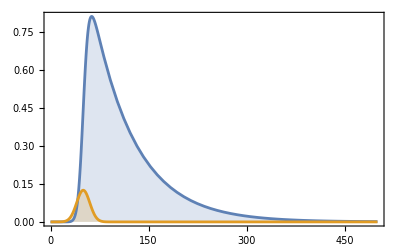

```mathematica
Plot[{Abs@xSol[t],Ω0[t,Θ0,τd,t0]},{t,0,500},Frame->True,Axes->None,FrameStyle->{{{20,Thickness[.003]},{20,Thickness[.003]}},{{20,Thickness[.003]},{20,Thickness[.003]}}},FrameTicksStyle->Directive[Black,Thick,FontSize->18,FontFamily->Times],PlotRangePadding->Scaled[.02],ImageSize->400,PlotRange->All,Filling->Axis]
```

```mathematica
eqnsSS={0==(I Ωσ) (y-yc)-γσ x,0==(I Ωσ) (2 x-1)-(I*Δ+γσ/2) y,0==(-I Ωσ) (2 x-1)+(I*Δ-γσ/2) yc};
```

```mathematica
Solve[eqnsSS,{x,y,yc}]
```

{{x→(16900 Ωσ^2)/(1+33800 Ωσ^2),y→-(130 ⅈ Ωσ)/(1+33800 Ωσ^2),yc→(130 ⅈ Ωσ)/(1+33800 Ωσ^2)}}

```mathematica
ThetaValues=π*Subdivide[0.0001,4,500];
AnalyticPulseArea={};
τ0=500;
```

```mathematica
Do[
eqnsΘ={x'[t]==(I Ω0[t,Θ0,τd,t0])/2 (y[t]-yc[t])-γσ x[t],y'[t]==(I Ω0[t,Θ0,τd,t0])/2 (2 x[t]-1)-(I*Δ+γσ/2) y[t],yc'[t]==(-I Ω0[t,Θ0,τd,t0])/2 (2 x[t]-1)+(I*Δ-γσ/2) yc[t]};
initialConditions={x[0]==0,y[0]==0,yc[0]==0};  
solAnalytic=NDSolve[{eqnsΘ,initialConditions},{x,y,yc},{t,-500,500}];  
xSolAnalytic[t_]=x[t]/. solAnalytic[[1]];
ySolAnalytic[t_]=y[t]/. solAnalytic[[1]];
ycSolAnalytic[t_]=yc[t]/. solAnalytic[[1]];
popintegrate=NIntegrate[xSolAnalytic[t],{t,-τ0,τ0}];
AppendTo[AnalyticPulseArea,{Θ0,popintegrate}]
,{Θ0,ThetaValues}]
```

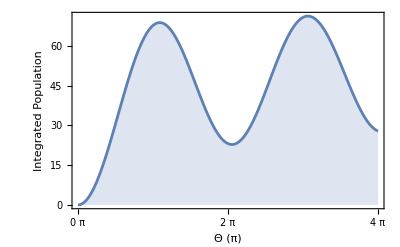

```mathematica
ListLinePlot[AnalyticPulseArea,AxesLabel->{"Θ (π)","Integrated Population"},Frame->True,Axes->None,FrameStyle->{{Directive[Black,Thickness[.003]],None},{None,Directive[Black,Thickness[.003]]}},FrameTicksStyle->Directive[Black,Thick,FontSize->18,FontFamily->"Times"],PlotRangePadding->Scaled[.02],ImageSize->400,PlotRange->All,Filling->Axis,FrameTicks->{Table[{k π,Row[{k," π"}]},{k,0,8}],Automatic}]
```

## Numerical solutions

```mathematica
Clear["Global`*"]
```

```mathematica
PartialTransposition[basis_,SubSystem_,rho_]:=Module[{indextb,indextbT,LenBas,TotalSystems,μ,ν,postb, rhoT},
indextb=Table[
Join[basis⟦j⟧,basis⟦k⟧],
{j,1,Length@basis},{k,1,Length@basis}];

indextbT=indextb;

TotalSystems=Length@basis⟦1⟧;

Do[
{μ,ν}={indextbT⟦i,k,SubSystem⟧,indextbT⟦i,k,SubSystem+TotalSystems⟧};
indextbT⟦i,k,SubSystem⟧=ν;
indextbT⟦i,k,SubSystem+TotalSystems⟧=μ;,
{i,1,Length@indextbT},
{k,1,Length@indextbT}];

postb=Table[
Position[indextb,indextbT⟦i,j⟧]⟦1⟧,
{i,1,Length@indextbT},
{j,1,Length@indextbT}];

rhoT=Table[
{μ,ν}=postb⟦i,j⟧;
rho⟦μ,ν⟧,
{i,1,Length@rho},
{j,1,Length@rho}];
rhoT]
```

```mathematica
basisfun[ntrun_,nmodes_,hilbertnumber_]:=Module[{basis,ntrunRev},ntrunRev=Reverse[ntrun];
basis=Flatten[Table[Reverse@Table[Subscript[i,k],{k,nmodes}],Evaluate[Sequence@@Table[{Subscript[i,k],0,ntrunRev[[k]]},{k,nmodes}]]],nmodes-1]];

destructionoperator[ntrun_,nmode_]:=Module[{ared,nmodes,hilbertred},nmodes=Length[ntrun];
hilbertred=ntrun[[nmode]]+1;
ared=SparseArray[{i_,j_}/;i-j==-1->Sqrt[j-1.],{hilbertred,hilbertred}];
If[nmodes>1,KroneckerProduct[Sequence@@Reverse@Table[If[i!=nmode,SparseArray@N@IdentityMatrix[ntrun[[i]]+1],ared],{i,nmodes}]],ared]];

Id[nn_]:=SparseArray[{i_,i_}->1,{nn,nn}];
```

```mathematica
NormalGrid[min_,max_,npoints_]:=Module[{grid},grid=Table[min+(max-min) (i-1)/(npoints-1),{i,1,npoints}];
grid]
LogGrid[lowerbound_,upperbound_,numpts_,accuracy_]:=Module[{grid,lb=Log[lowerbound],ub=Log[upperbound]},grid=Rationalize[#,0]&/@Table[Exp[mPb],{mPb,lb,ub,(ub-lb)/(numpts-1)}];
If[accuracy!=0,Round[grid,accuracy],grid]]
```

## Solving the master equation - Time dependence

```mathematica
ntrun={1};
nmodes=Length@ntrun;
```

```mathematica
TLSPulsedDynamics[τd_,t0_,Θ0_,γσ_,Δσ_,τ0_]:=Module[{hilbertnumber,basis,σ,σd,σx,σy,σz,Ω,H,Op,Par,Opp,M,ρ,ρini,Sol,ρreshape,nX,nσx,nσy,nσz},
hilbertnumber=Product[ntrun[[i]]+1,{i,nmodes}];
basis=basisfun[ntrun,nmodes,hilbertnumber];
σ=destructionoperator[ntrun,1];
σd=σᵀ;
σx=(σ+σd);
σy=I (σ-σd);
σz=σd.σ-σ.σd;
Ω[t_,Θ_,σ_,tc_]:=Θ/Sqrt[2 π σ^2] Exp[-(t-tc)^2/(2 σ^2)];
H=Δσ σd.σ+Ω[t,Θ0,τd,t0]/2 (σ+σd);
Op={σ};
Par={γσ};
Opp=ConjugateTranspose[#]&/@Op;
M=-I (KroneckerProduct[H,IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Transpose[H]])+Sum[1/2 Par[[i]] (2 KroneckerProduct[Op[[i]],Op[[i]]]-KroneckerProduct[Opp[[i]].Op[[i]],IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Opp[[i]].Op[[i]]]),{i,1,Length@Par}];
ρ[t_]=Flatten[Table[ρ[n,m][t],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],1];
ρini=Flatten[Table[ρ[n,m][0]==KroneckerDelta[n,0] KroneckerDelta[m,0],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],2];
Sol=Flatten@NDSolve[{ρ'[t]==M.ρ[t],ρini},ρ[t],{t,-τ0,τ0}];
ρreshape=ArrayReshape[(ρ[t]/. Sol)/. t->τ,{hilbertnumber,hilbertnumber}];
nX=Re@Tr[(σd.σ).ρreshape];
nσx=Re@Tr[(σx).ρreshape];
nσy=Re@Tr[(σy).ρreshape];
nσz=Re@Tr[(σz).ρreshape];
{nX,nσx,nσy,nσz}]
```

```mathematica
τd=10; (*ps*)
t0=50; (*ps*)
Θ0=π;
γσ=1/65; (*ps^-1*)
Δσ=0;
τ0=500;
```

```mathematica
{nX,nσx,nσy,nσz}=TLSPulsedDynamics[τd,t0,Θ0,γσ,Δσ,τ0];
```

```mathematica
NIntegrate[nX,{τ,0,τ0}]
```

67.685

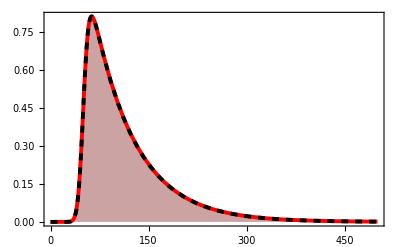

```mathematica
Plot[{nX,Abs@xSol[τ]},{τ,0,τ0},PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007],Dashed]},Frame->True,Axes->None,FrameStyle->{{{20,Thickness[.003]},{20,Thickness[.003]}},{{20,Thickness[.003]},{20,Thickness[.003]}}},FrameTicksStyle->Directive[Black,Thick,FontSize->18,FontFamily->Times],PlotRangePadding->Scaled[.02],ImageSize->400,PlotRange->All,Filling->Axis]
```

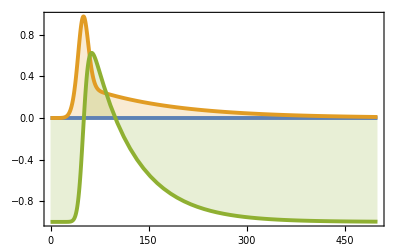

```mathematica
Plot[{nσx,nσy,nσz},{τ,0,τ0},PlotStyle->{Directive[Thickness[0.007]]},Frame->True,Axes->None,FrameStyle->{{{20,Thickness[.003]},{20,Thickness[.003]}},{{20,Thickness[.003]},{20,Thickness[.003]}}},FrameTicksStyle->Directive[Black,Thick,FontSize->18,FontFamily->Times],PlotRangePadding->Scaled[.02],ImageSize->400,PlotRange->All,Filling->Axis]
```

## Solving the master equation - Pulse area dependence

```mathematica
ntrun={1};
nmodes=Length@ntrun;
```

```mathematica
τd=10; (*ps*)
t0=50; (*ps*)
Θ0=π;
γσ=1/65; (*ps^-1*)
Δσ=0;
τ0=500;
ThetaValues=π*Subdivide[0.0001,8,500];
```

```mathematica
RabiPulseArea[τd_,t0_,Θ0_,γσ_,Δσ_,τ0_]:=Module[{hilbertnumber,basis,σ,σd,Ω,H,Op,Par,Opp,M,ρ,ρini,Sol,ρreshape,nX,intpopulations},
hilbertnumber=Product[ntrun[[i]]+1,{i,nmodes}];
basis=basisfun[ntrun,nmodes,hilbertnumber];
σ=destructionoperator[ntrun,1];
σd=σᵀ;
Ω[t_,Θ_,σ_,tc_]:=Θ/Sqrt[2 π σ^2] Exp[-(t-tc)^2/(2 σ^2)];
H=Δσ σd.σ+Ω[t,Θ0,τd,t0]/2 (σ+σd);
Op={σ};
Par={γσ};
Opp=ConjugateTranspose[#]&/@Op;
M=-I (KroneckerProduct[H,IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Transpose[H]])+Sum[1/2 Par[[i]] (2 KroneckerProduct[Op[[i]],Op[[i]]]-KroneckerProduct[Opp[[i]].Op[[i]],IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Opp[[i]].Op[[i]]]),{i,1,Length@Par}];
ρ[t_]=Flatten[Table[ρ[n,m][t],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],1];
ρini=Flatten[Table[ρ[n,m][0]==KroneckerDelta[n,0] KroneckerDelta[m,0],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],2];
Sol=Flatten@NDSolve[{ρ'[t]==M.ρ[t],ρini},ρ[t],{t,-τ0,τ0}];
ρreshape=ArrayReshape[(ρ[t]/. Sol)/. t->τ,{hilbertnumber,hilbertnumber}];
nX=Re@Tr[(σd.σ).ρreshape];
intpopulations=NIntegrate[nX,{τ,-τ0,τ0}];
{nX,intpopulations}]
```

```mathematica
{nX,Intpop}=RabiPulseArea[τd,t0,Θ0,γσ,Δσ,τ0];
```

```mathematica
Intpop
```

67.685

```mathematica
RabiPulseAreaIteration[τd_,t0_,γσ_,Δσ_,τ0_,ThetaValues_]:=Module[{hilbertnumber,basis,σ,σd,Ω,H,Op,Par,Opp,M,ρ,ρini,Sol,ρreshape,nX,intpopulations,results={}},hilbertnumber=Product[ntrun[[i]]+1,{i,nmodes}];
basis=basisfun[ntrun,nmodes,hilbertnumber];
σ=destructionoperator[ntrun,1];
σd=σᵀ;
Do[Ω[t_,Θ_,σ_,tc_]:=Θ/Sqrt[2 π σ^2] Exp[-(t-tc)^2/(2 σ^2)];
H=Δσ σd.σ+Ω[t,Θ0,τd,t0]/2 (σ+σd);
Op={σ};
Par={γσ};
Opp=ConjugateTranspose[#]&/@Op;
M=-I (KroneckerProduct[H,IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Transpose[H]])+Sum[1/2 Par[[i]] (2 KroneckerProduct[Op[[i]],Op[[i]]]-KroneckerProduct[Opp[[i]].Op[[i]],IdentityMatrix[hilbertnumber]]-KroneckerProduct[IdentityMatrix[hilbertnumber],Opp[[i]].Op[[i]]]),{i,1,Length@Par}];
ρ[t_]=Flatten[Table[ρ[n,m][t],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],1];
ρini=Flatten[Table[ρ[n,m][0]==KroneckerDelta[n,0] KroneckerDelta[m,0],{n,0,hilbertnumber-1},{m,0,hilbertnumber-1}],2];
Sol=Flatten@NDSolve[{ρ'[t]==M.ρ[t],ρini},ρ[t],{t,-τ0,τ0}];
ρreshape=ArrayReshape[(ρ[t]/. Sol)/. t->τ,{hilbertnumber,hilbertnumber}];
nX=Re@Tr[(σd.σ).ρreshape];
intpopulations=NIntegrate[nX,{τ,0,τ0}];
AppendTo[results,{Θ0,intpopulations}],{Θ0,ThetaValues}];
results]
```

```mathematica
results=RabiPulseAreaIteration[τd,t0,γσ,Δσ,τ0,ThetaValues];
```

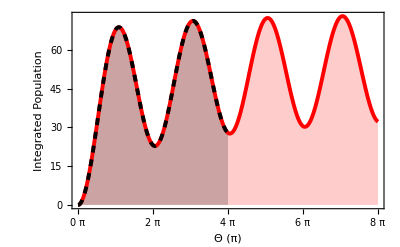

```mathematica
ListLinePlot[{results,AnalyticPulseArea},PlotStyle->{Directive[Thickness[0.007],Red],Directive[Thickness[0.007],Black, Dashed]},AxesLabel->{"Θ (π)","Integrated Population"},Frame->True,Axes->None,FrameStyle->{{Directive[Black,Thickness[.003]],None},{None,Directive[Black,Thickness[.003]]}},FrameTicksStyle->Directive[Black,Thick,FontSize->18,FontFamily->"Times"],PlotRangePadding->Scaled[.02],ImageSize->400,PlotRange->All,Filling->Axis,FrameTicks->{Table[{k π,Row[{k," π"}]},{k,0,8}],Automatic}]
```